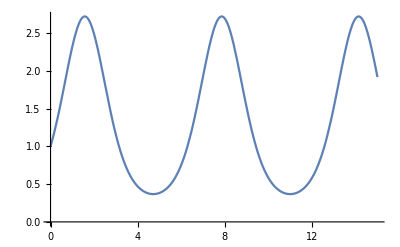

```mathematica
(*Quiz1 was easy so I didn't write out solutions...*)
(*Here is quiz 2*)
(*2.1*)
Plot[E^Sin[z],{z,0,15}]
```

```mathematica
(*2.2*)
series1 = Series[E^Sin[z],{z,0,10}]
```

1+z+z^2/2-z^4/8-z^5/15-z^6/240+z^7/90+(31 z^8)/5760+z^9/5670-(2951 z^10)/3628800+O[z]^11

```mathematica
(*2.3*)
Coefficient[(1+a*x+b*x^2)^6,x^5]
```

6 a^5+60 a^3 b+60 a b^2

```mathematica
(*2.4*)
(*remember... Cos[θ]=(v1·v2)/(|v1| |v2|)*)
v1={1,2,3}
v2={-2,5,-1}
dotproduct=v1.v2
magv1=Sqrt[v1.v1]
magv2=Sqrt[v2.v2]
N[ArcCos[dotproduct/(magv1 magv2)]]
(*answer is in radians*)
```

{1,2,3}

{-2,5,-1}

5

√14

√30

1.32433

```mathematica
(*2.5*)
left={{3,2},{4,-1}}
right = {-1,0}
sol = Inverse[left].right
Matrixform[sol]
(*x=-1/11 and y=4/11*)
```

{{3,2},{4,-1}}

{-1,0}

{-1/11,-4/11}

Matrixform[{-1/11,-4/11}]

```mathematica
(*2.6*)
(*Compound interest +5% annual*)
TableForm[Table[{t,P(1+.05)^t},{t,1,30}]]
```

1 | 1.05 P
2 | 1.1025 P
3 | 1.15763 P
4 | 1.21551 P
5 | 1.27628 P
6 | 1.3401 P
7 | 1.4071 P
8 | 1.47746 P
9 | 1.55133 P
10 | 1.62889 P
11 | 1.71034 P
12 | 1.79586 P
13 | 1.88565 P
14 | 1.97993 P
15 | 2.07893 P
16 | 2.18287 P
17 | 2.29202 P
18 | 2.40662 P
19 | 2.52695 P
20 | 2.6533 P
21 | 2.78596 P
22 | 2.92526 P
23 | 3.07152 P
24 | 3.2251 P
25 | 3.38635 P
26 | 3.55567 P
27 | 3.73346 P
28 | 3.92013 P
29 | 4.11614 P
30 | 4.32194 P

```mathematica
(*2.7*)
Integrate[Sin[a t]^2 E^(-s t),{t,0,∞}]
```

ConditionalExpression[(2 a^2)/(4 a^2 s+s^3), 2 Im[a]<Re[s]&&2 Im[a]+Re[s]>0]

```mathematica
(*2.8*)
(*equation 1*)
Integrate[Sqrt[(x^2)-(a^2)]/(x^2),x]
Simplify[D[%,x]]
(*equation 2*)
Integrate[1/(Sin[ax]^2 * Cos[ax]),x]
Simplify[D[%,x]]
```

-(√(-a^2+x^2) (a √(1-x^2/a^2)+x ArcSin[x/a]))/(a x √(1-x^2/a^2))

(√(-a^2+x^2))/x^2

x Csc[ax]^2 Sec[ax]

Csc[ax]^2 Sec[ax]